```mathematica
ClearAll["Global`*"]
```

```mathematica
L=2;
h=1;
```

```mathematica
(*test case 1*)
```

```mathematica
(*I choose an exact solution on sub_mesh[1]*)
u1[x_]:=1+x^2+2 h^2
(*I chose an exact solution on sub_mesh[0] that matches u1 when y -> h*)
u0[x_,y_]:=(1+x^2 + 2y^2) * Cos[2 π y/h]
```

```mathematica
Grad[u0[x,y],{x,y}]//FullSimplify
```

{2 x Cos[2 π y],4 y Cos[2 π y]-2 π (1+x^2+2 y^2) Sin[2 π y]}

```mathematica
Laplacian[u0[x,y],{x,y}]//FullSimplify
```

-2 (-3+2 π^2 (1+x^2+2 y^2)) Cos[2 π y]-16 π y Sin[2 π y]

```mathematica
FullSimplify[u1'[x]]
```

2 x

```mathematica
(*check for u0,u1*)
```

```mathematica
t0=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_0.csv"];
t0=Table[{t0[[i,2]],t0[[i,3]],t0[[i,1]]},{i,2,Length[t0]}]
```

```mathematica
t1=Import["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/u_1.csv"];
t1=Table[{t1[[i,2]],t1[[i,3]],t1[[i,1]]},{i,2,Length[t1]}]
```

```mathematica
δ0=Max[Table[Abs[t0[[i,3]]-u0[t0[[i,1]],t0[[i,2]]]],{i,1,Length[t0]}]]
δ1=Max[Table[Abs[t1[[i,3]]-u1[t1[[i,1]]]],{i,1,Length[t1]}]]
Max[δ0,δ1]
```

7.89292×10^-6

2.1875×10^-6

7.89292×10^-6

-Graphics3D-

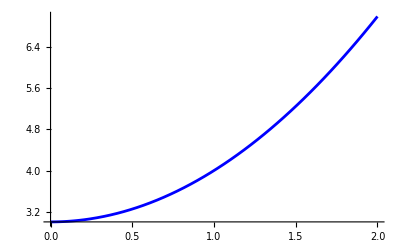

```mathematica
plotexact0=Plot3D[u0[x,y],{x,0,L},{y,0,h},PlotRange->Full,PlotStyle->{Blue,Opacity[0.1]}]
plotexact1=Plot[u1[x],{x,0,L},PlotRange->Full,PlotStyle->{Blue,Opacity[1]}]
```

```mathematica
plotnum0=ListPointPlot3D[t0,PlotRange->Full,PlotStyle->Red,AspectRatio->Automatic]
```

-Graphics3D-

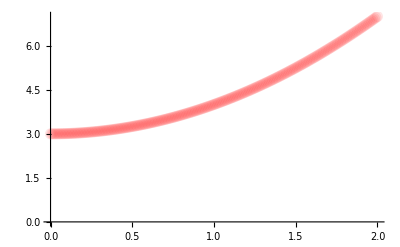

```mathematica
plotnum1=ListPlot[Table[{t1[[i,1]],t1[[i,3]]},{i,1,Length[t1]}],PlotRange->Full,PlotStyle->{Red,Opacity[0.1],PointSize[0.02]}]
```

```mathematica
Show[plotexact0,plotnum0]
```

-Graphics3D-

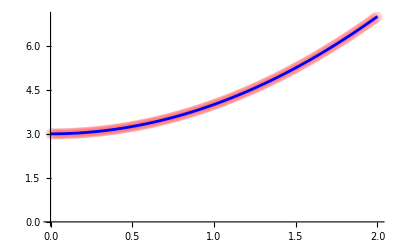

```mathematica
Show[plotnum1,plotexact1]
```